General::munfl: Csch[1848.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

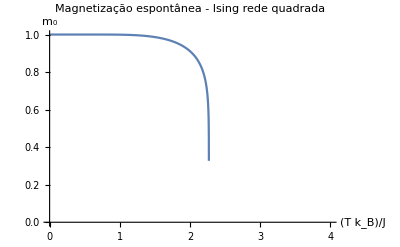

```mathematica
m0 [T_] := (1 - (Sinh[2/T])^(-4))^(1/8)

Plot[{m0[T]},{T,0.001,4},AxesLabel->{T Subscript[k,B]/J,Subscript[m,0]}, PlotLabel->"Magnetização espontânea - Ising rede quadrada ",PlotRange->{{0,4},{0,1}}]
```